```mathematica
DIFFUSION[x_,t_]:=NIntegrate[(4*π*t)^(-1/2)*Exp[-(x-y)^2*(4*t)^(-1)],{y,-1,1}]
```

```mathematica
DIFFUSION[1,0.0001]
```

0.5

NIntegrate::ncvb: NIntegrateが{y} = {0.33206233328106477`}の近傍のyで二分法を9回反復しましたが，指定された確度に収束しませんでした．NIntegrateは積分と誤差推定として0.と0.を得ました．

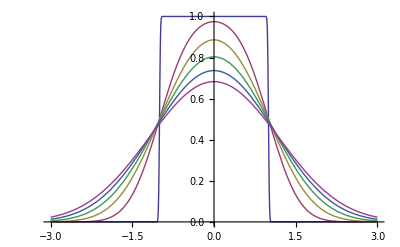

```mathematica
Plot[{DIFFUSION[x,0.0001],DIFFUSION[x,0.1],DIFFUSION[x,0.2],DIFFUSION[x,0.3],DIFFUSION[x,0.4],DIFFUSION[x,0.5]},{x,-3,3}]
```